```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
```

```mathematica
f[x_,t_]:=Piecewise[{{10,0<=x<t},{-2x+2t+10,t<=x<4},{2t+2,4<=x<=5}}]
g[x_,t_]:=Piecewise[{{10,0<=x<t},{x+10-t,t<=x<3},{-2x+19-t,3<=x<4},{11-t,4<=x<=5}}]
h[x_,t_]:=Piecewise[{{Evaluate[f[x,t]],3<=t<=4},{Evaluate[g[x,t]],1<=t<3}}]
```

```mathematica
Manipulate[Plot[{h[x,t],10},{x,0,5},PlotRange->{6,15}],{t,4,1}]
```

```mathematica
RD1[x_,t_]:=Piecewise[{{10,0<=x<t},{-4x+10+4t,t<=x<=4}}]
MD[x_,t_]:=Piecewise[{{10,0<=x<t},{-3x+10+3t,t<=x<3},{-4x+13+3t,3<=x<=4}}]
KD[x_,t_]:=Piecewise[{{10,0<=x<t},{-6x+10+6t,t<=x<2},{-3x+4+6t,2<=x<3},{-4x+7+6t,3<=x<=4}}]
RD2[x_,t_]:=Piecewise[{{10,0<=x<t},{-4x+10+4t,t<=x<1},{-6x+12+4t,1<=x<2},{-3x+6+4t,2<=x<3},{-4x+9+4t,3<=x<=4}}]
P[x_,t_]:=Piecewise[{{Evaluate[RD1[x,t]],3<=t<=4},{Evaluate[MD[x,t]],2<=t<3},{Evaluate[KD[x,t]],1<=t<2},{Evaluate[RD2[x,t]],0<=t<1}}]
GW[x_,t_]:=Piecewise[{{5,0<=x<t},{-4x+4t+5,t<=x<=4}}]
```

```mathematica
Manipulate[Plot[{P[x,t],GW[x,t],10},{x,0,4},PlotRange->{-15,15}],{t,4,0}]
```

```mathematica
G[gstar1_, gstar2_]:=(gstar1/106.75)(gstar2/106.75)^(-4/3) 
fΔ[gstar1Δ_, gstar2Δ_, TΔ_]:= (2.7*10^-6)*(gstar1Δ/106.75)^(1/2)*(gstar2Δ/106.75)^(-1/3)*(TΔ/10^2);
fKD[gstar1Δ_, gstar2Δ_,ρKD_, NKD_]:= (1.1*10^-3)*G[gstar1Δ, gstar2Δ]^(1/4)*(ρKD^(1/4)/(10*10^3))*(Exp[NKD]/10);
ΩGWsth2[gstar1k_, gstar2k_, Einf_]:=G[gstar1k, gstar2k]*(1.3*10^-17)*(Einf/10^16)^4;
fdom[gstar1Δ_, gstar2Δ_,ρKD_,ρdom_, NKD_]:= fKD[gstar1Δ, gstar2Δ,ρKD, NKD]*(ρdom/ρKD)^(1/6);
ΩGWh2[gstar1k_, gstar2k_,gstar1Δ_, gstar2Δ_, TΔ_,ρKD_,ρdom_, NKD_,  Einf_,f_]:= ΩGWsth2[gstar1k, gstar2k, Einf]*
Piecewise[{{1, f<fΔ[gstar1Δ, gstar2Δ, TΔ]}, {f/fΔ[gstar1Δ, gstar2Δ, TΔ], fΔ[gstar1Δ, gstar2Δ, TΔ]<f<fKD[gstar1Δ, gstar2Δ,ρKD, NKD]}, {(fKD[gstar1Δ, gstar2Δ,ρKD, NKD]/fΔ[gstar1Δ, gstar2Δ, TΔ])(fKD[gstar1Δ, gstar2Δ,ρKD, NKD]/f)^2, fKD[gstar1Δ, gstar2Δ,ρKD, NKD]<f<fdom[gstar1Δ, gstar2Δ,ρKD,ρdom, NKD]}, {(fKD[gstar1Δ, gstar2Δ,ρKD, NKD]/fΔ[gstar1Δ, gstar2Δ, TΔ])(fKD[gstar1Δ, gstar2Δ,ρKD, NKD]/fdom[gstar1Δ, gstar2Δ,ρKD,ρdom, NKD])^2, fdom[gstar1Δ, gstar2Δ,ρKD,ρdom, NKD]<f}}]
```

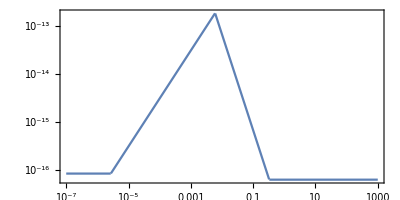

```mathematica
LogLogPlot[{ΩGWh2[106.75, 106.75,106.75, 106.75, 10^2,(10*10^3)^4,Exp[6*4]*(10*10^3)^4(*ρdom = Exp[6NKD]*ρKD*),4, 1.6 10^16,f]},{f,10^-7,10^3} , PlotRange-> Full, Frame-> True, AspectRatio-> 0.5]
```

```mathematica
Subscript[M, p]=2.4*10^18;
ρdom=Exp[6*4]*(10*10^3)^4;
ρKD=(10*10^3)^4;
NKD=4;
c=3*10^8;
```

```mathematica
fdom1=fdom[106.75, 106.75,(10*10^3)^4,Exp[6*4]*(10*10^3)^4,4];
fKD1=fKD[106.75, 106.75,(10*10^3)^4,4];
fΔ1=fΔ[106.75, 106.75,100];
Ωini[f_]:=ΩGWsth2[106.75, 106.75, 1.6 10^16]+10^-10 f^8;
```

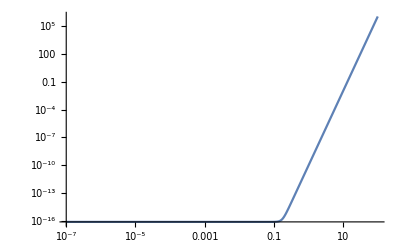

```mathematica
LogLogPlot[Ωini[f],{f,10^-7,100}, PlotRange->All]
```

```mathematica
a[f_,ft_]:=Piecewise[{{Ωini[f](ft/fdom1)^2,f>=fdom1},{Ωini[f](ft/f)^2,ft<=f<fdom1},{Ωini,f<ft}}];
b[f_,ft_]:=Piecewise[{{Ωini[f](fKD1/ft)(fKD1/fdom1)^2,f>=fdom1},{Ωini[f](fKD1/ft)(fKD1/f)^2,fKD1<=f<fdom1},{Ωini[f](f/ft),ft<=f<fKD1},{Ωini,f<ft}}];
d[f_,ft_]:=Piecewise[{{Evaluate[a[f,ft]],ft>=fKD1},{Evaluate[b[f,ft]],ft<fKD1}}];
```

```mathematica
Manipulate[LogLogPlot[d[f,ft],{f,10^-7,1},PlotRange->{10^-30,10^-3},PlotPoints->100],{ft,fdom1,10^-5}]
```